```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}",
"\\definecolor{Black}{HTML}{000000}",
"\\definecolor{White}{HTML}{FFFFFF}"},
"FontSize" -> 16];
```

```mathematica
ClearAll[v12, vb]
v12[v1_, v2_, c_] := c Det[{v2,v1}]/Det[{c, v1-v2}]
vb[v1_, v2_, c_] := v2 Det[{v1,c}]/Det[{v2, c - v1}]
```

```mathematica
ClearAll[gl]
gl = DynamicModule[
{
v1 = {5,1},
v2 = {3,5},
o = {0,0},
c = {3,1.5}
},
(*Column[{*)
Graphics[
{
Locator[Dynamic[v1]],
Locator[Dynamic[v2]],
PointSize -> Large,
Point[o],
Locator[Dynamic[c]],
Line[{o,Dynamic[v1]}],
Line[{o,Dynamic[v2]}],
Line[{Dynamic[v1],Dynamic[v2]}],
Line[{o, Dynamic[v12[v1, v2, c]]}],
Line[{Dynamic[v1], Dynamic[vb[v1, v2, c]]}],
Line[{Dynamic[v2], Dynamic[vb[v2, v1, c]]}]
},PlotRange->{{-1,6},{-1,6}}
](*,Dynamic[c], Dynamic[v1],Dynamic[v2]
}]*)
 ]
```

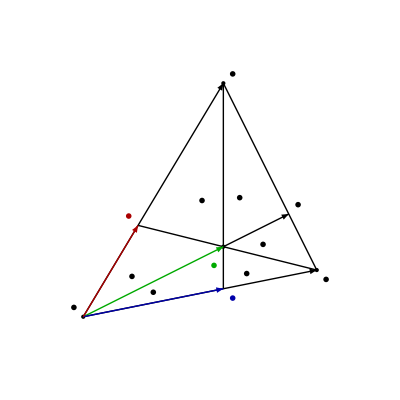

```mathematica
g = Module[
{
v1 = {5,1},
v2 = {3,5},
o = {0,0},
e1 = {1,0},
e2 = {0,1},
c = {3,1.5},
d,e,f
},
e = v12[v1, v2, c];
f = vb[v1, v2, c];
d = vb[v2, v1, c];
Graphics[
{
PointSize -> Large,
Point[o],
Point[c],
Point[v1],
Point[v2],

Text[MaTeX["A_1"], (c+d)/4],
Text[MaTeX["A_2"], d + (c-d)/4 + (v1-d)/4],
Text[MaTeX["A_3"], c+ (e-c)/4 + (v1-c)/4],
Text[MaTeX["A_4"], c+ (e-c)/4 + (v2-c)/4],
Text[MaTeX["A_5"], c+ (f-c)/4 + (v2-c)/4],
Text[MaTeX["A_6"], (c+ f)/4],

Text[MaTeX["\\mathbf{O}"], o-0.2 e1 + 0.2 e2],
Text[MaTeX["\\mathbf{A}"], v1 + 0.2 (e1-e2)],
Text[MaTeX["\\mathbf{B}"], v2 + 0.2 (e1 + e2)],
Text[MaTeX["\\mathbf{E}"], e + 0.2 (e1 +e2)],

Arrow[{o,v1}],
Arrow[{o,v2}],
Line[{v1,v2}],

Line[{v2, d}],
Line[{v1, f}],
Arrow[{c,e}],

Green//Darker,
Arrow[{o,c}],
Text[MaTeX["\\color{GreenDarker}\\mathbf{C}"], c + 0.2 (-e1 - 2 e2)],

Blue//Darker,
Arrow[{o, d}],
Text[MaTeX["\\color{BlueDarker}\\mathbf{D}"], d+ 0.2 (e1 -e2)],

Red //Darker,
Arrow[{o, f}],
Text[MaTeX["\\color{RedDarker}\\mathbf{F}"], f + 0.2 (-e1 +e2)]
},PlotRange->{{-1,6},{-1,6}}
]
 ]
```

```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
(*Export["tmp/triangle.pdf",g]*)
peeters`exportForLatex["triangle_area_problemFig1",g]
```

{triangle_area_problemFig1.eps,triangle_area_problemFig1pn.png}

```mathematica
Directory[]
```

/Users/pjoot

```mathematica
ClearAll[a,b,c,d, x, y, z, s]
a = 40;
b = 30;
c = 35;
d = 84;
s = {4 a^2 (x - z)^2 == z^2 y^2, 4 b^2 (x - z)^2 == z^2 (x - y - z)^2,
4 c^2 (z + y)^2 == z^2 (x - y - z)^2,
4 d^2 (x - y)^2 == y^2 (x - y - z)^2
}
ss = Solve[s, {x, y, z}]
```

{6400 (x-z)^2==y^2 z^2,3600 (x-z)^2==(x-y-z)^2 z^2,4900 (y+z)^2==(x-y-z)^2 z^2,28224 (x-y)^2==y^2 (x-y-z)^2}

{{x→-630,y→-280,z→-140},{x→0,y→0,z→0},{x→630,y→280,z→140}}

```mathematica
630/2
```

315